## Boltzmann weights for the random unitary channel

Minimal setup: the 2nd Renyi entropy in the n=2, q -> ∞  limit corresponds to the partition function of the 2D Ising model (σ = 0,1) on a honeycomb lattice with diagonal bonds w_d and vertical bond w_g. Integrating out the top spin value on the vertical bonds gives an Ising model on a triangular lattice with diagonal bonds and horizontal bonds, or equivalently one can think of it as weights defined on the inverted triangles with spins on each vertex σ_1 (left), σ_2(right) and σ_3 (bottom).

### The 3-body Boltzmann weight

The Weingarten function is on the 2-Unitary is w_g(σ_3 τ^-1,q)=(δ_(σ_3 τ^-1,0))/(q^2-1)-(δ_(σ_3 τ^-1,1))/(q(q^2-1)). For the n=2 case, δ_(σ_3 τ^-1,1) can be subbed by δ_(σ_3,τ) and δ_(σ_3 τ^-1,-1) by  1-δ_(σ_3,τ). The Weingarten function will enter the diagonal bond weight as well: w_d(σ,τ,q,p,Γ)=(q^(|στ^-1|)(1-p)^2+qp^2)(1-Γ)^2 +w_g(στ^-1,q)q^(|τ|+1)(q^(|σ|-1)(1-p)^2+p^2)Γ^2, where q is the local Hilbert space dimension, p is the probability of measurement,  Γ is the dissipation rate, |·| is the number of cycles of the element, which will be 1 when the argument is transposition (denoted as -1) and 2 when the argument is the identity (denoted as +1).
In the following cell, we assume that

```mathematica
wg[c_,τ_,q_]:= KroneckerDelta[c,τ]/(q^2-1) -(1- KroneckerDelta[c,τ])/(q(q^2-1) );
wd[a_,τ_,q_,p_,Γ_]:= ((q^2 *KroneckerDelta[a,τ]+q (1-KroneckerDelta[a,τ]))(1-p)^2+q p^2) (1-Γ)^2 + wg[a,τ,q](q^3 *KroneckerDelta[τ,1]+q^2 *KroneckerDelta[τ,-1])((q KroneckerDelta[a,1]+ KroneckerDelta[a,-1])(1-p)^2 + p^2) Γ^2
```

The three body weight is then w^(3)(σ_1,σ_2,σ_3,q,p)=∑_τ | w_d(σ_1,τ,q,p,Γ)w_d(σ_2,τ,q,p,Γ)w_g(σ_3 τ^-1,q^2).

```mathematica
w3[a_,b_,c_,q_,p_,Γ_]:=wd[a,1,q,p,Γ] wd[b,1,q,p,Γ]wg[c,1,q^2]+wd[a,-1,q,p,Γ] wd[b,-1,q,p,Γ]wg[c,-1,q^2]
```

### Evaluate all the combinations of {σ_1,σ_2,σ_3} up to the highest order

First, we check that that the σ_1 and  σ_2 are symmetric:

```mathematica
Clear[q,p,Γ]
w3[-1,1,1,q,p,Γ]-w3[1,-1,1,q,p,Γ]
w3[-1,1,-1,q,p,Γ]-w3[1,-1,-1,q,p,Γ]
```

0

0

Then we check that that the replica symmetry is broken. E.g., The following is non-zero:

```mathematica
Simplify[w3[1,1,1,q,p,Γ]-w3[-1,-1,-1,q,p,Γ]]
```

1/(-1+q^4)((1-2 p+2 p^2)^2 ((-1+Γ)^2-(q Γ^2)/(-1+q^2))^2-q^2 ((p^2+(-1+p)^2 q) (-1+Γ)^2+((1-2 p+2 p^2) q Γ^2)/(-1+q^2))^2-(((1-2 p+2 p^2) q (-1+Γ)^2-(q (p^2+(-1+p)^2 q) Γ^2)/(-1+q^2))^2)/q^2+(q^2 (q-2 p q+p^2 (1+q))^2 ((-1+Γ)^2+q^2 (-1+2 Γ-2 Γ^2))^2)/((-1+q^2)^2))

We take all the weights and multiply by a common denominator, which is q^4+1. The weight of all spin up configuration in a triangle:

```mathematica
w3[1,1,1,q,p,Γ]
```

-((((1-p)^2 q+p^2 q) (1-Γ)^2-(q (p^2+(1-p)^2 q) Γ^2)/(-1+q^2))^2)/(q^2 (-1+q^4))+(((p^2 q+(1-p)^2 q^2) (1-Γ)^2+(q^3 (p^2+(1-p)^2 q) Γ^2)/(-1+q^2))^2)/(-1+q^4)

Now we take the numerator. Note that we need to take off a factor of q^2 in the numerator of in the first term :

```mathematica
Expand[-(((1-p)^2 +p^2 ) (1-Γ)^2-((p^2+(1-p)^2 q) Γ^2)/(-1+q^2))^2+((p^2 q+(1-p)^2 q^2) (1-Γ)^2+(q^3 (p^2+(1-p)^2 q) Γ^2)/(-1+q^2))^2,q]
```

-((1-p)^2+p^2)^2 (1-Γ)^4+p^4 q^2 (1-Γ)^4+2 (1-p)^2 p^2 q^3 (1-Γ)^4+(1-p)^4 q^4 (1-Γ)^4+(2 p^2 ((1-p)^2+p^2) (1-Γ)^2 Γ^2)/(-1+q^2)+(2 (1-p)^2 ((1-p)^2+p^2) q (1-Γ)^2 Γ^2)/(-1+q^2)+(2 p^4 q^4 (1-Γ)^2 Γ^2)/(-1+q^2)+(4 (1-p)^2 p^2 q^5 (1-Γ)^2 Γ^2)/(-1+q^2)+(2 (1-p)^4 q^6 (1-Γ)^2 Γ^2)/(-1+q^2)-(p^4 Γ^4)/((-1+q^2)^2)-(2 (1-p)^2 p^2 q Γ^4)/((-1+q^2)^2)-((1-p)^4 q^2 Γ^4)/((-1+q^2)^2)+(p^4 q^6 Γ^4)/((-1+q^2)^2)+(2 (1-p)^2 p^2 q^7 Γ^4)/((-1+q^2)^2)+((1-p)^4 q^8 Γ^4)/((-1+q^2)^2)

Now do the same for all spin down configuration:

```mathematica
w3[-1,-1,-1,q,p,Γ]
```

-((((1-p)^2 q+p^2 q) (1-Γ)^2-(((1-p)^2+p^2) q^2 Γ^2)/(-1+q^2))^2)/(q^2 (-1+q^4))+(((p^2 q+(1-p)^2 q^2) (1-Γ)^2+(((1-p)^2+p^2) q^2 Γ^2)/(-1+q^2))^2)/(-1+q^4)

```mathematica
Expand[-(((1-p)^2 +p^2 ) (1-Γ)^2-(((1-p)^2+p^2) q Γ^2)/(-1+q^2))^2+((p^2 q+(1-p)^2 q^2) (1-Γ)^2+(((1-p)^2+p^2) q^2 Γ^2)/(-1+q^2))^2,q]
```

-((1-p)^2+p^2)^2 (1-Γ)^4+p^4 q^2 (1-Γ)^4+2 (1-p)^2 p^2 q^3 (1-Γ)^4+(1-p)^4 q^4 (1-Γ)^4+(2 ((1-p)^2+p^2)^2 q (1-Γ)^2 Γ^2)/(-1+q^2)+(2 p^2 ((1-p)^2+p^2) q^3 (1-Γ)^2 Γ^2)/(-1+q^2)+(2 (1-p)^2 ((1-p)^2+p^2) q^4 (1-Γ)^2 Γ^2)/(-1+q^2)-(((1-p)^2+p^2)^2 q^2 Γ^4)/((-1+q^2)^2)+(((1-p)^2+p^2)^2 q^4 Γ^4)/((-1+q^2)^2)

It’s pretty clear the leading term in both cases has q^4 power, but  (q^4-1)w^(3)(+1,+1,+1)=(1-p)^4 q^4 (1-Γ)^4+(2 (1-p)^4 q^6 (1-Γ)^2 Γ^2)/(-1+q^2)+((1-p)^4 q^8 Γ^4)/((-1+q^2)^2), whereas (q^4-1)w^(3)(-1,-1,-1)=(1-p)^4 q^4 (1-Γ)^4.
 Just like the previous the previous dissipation we considered, the dissipative term is the symmetry breaking term.

Applying the same to other weights,  we gather all the results here,
(q^4-1)w^(3)(-1,-1,1)=2 (1-p)^2 p^2 q^2 (1-Γ)^4+p^4 q^2 (1-Γ)^4,
(q^4-1)w^(3)(1,1,-1)=2 (1-p)^2 p^2 q^2 (1-Γ)^4+p^4 q^2 (1-Γ)^4-(2 (1-p)^4 q^4 (1-Γ)^2 Γ^2)/(-1+q^2)-((1-p)^4 q^6 Γ^4)/((-1+q^2)^2)=2 (1-p)^2 p^2 q^2 (1-Γ)^4+p^4 q^2 (1-Γ)^4-2 (1-p)^4 q^2 (1-Γ)^2 Γ^2-(1-p)^4 q^2 Γ^4
(q^4-1)w^(3)(-1,1,1)=(q^4-1)w^(3)(1,-1,1)=(1-p)^4 q^3 (1-Γ)^4+(1-p)^2 p^2 q^3 (1-Γ)^4 +((1-p)^4 q^5 (1-Γ)^2 Γ^2)/(-1+q^2)=(1-p)^4 q^3 (1-Γ)^4+(1-p)^2 p^2 q^3 (1-Γ)^4+(1-p)^4 q^3 (1-Γ)^2 Γ^2+(1-p)^2 p^2 q^3 (1-Γ)^2 Γ^2, 
(q^4-1)w^(3)(-1,1,-1)=(q^4-1)w^(3)(1,-1,-1)=(1-p)^4 q^3 (1-Γ)^4+(1-p)^2 p^2 q^3 (1-Γ)^4.
Now use the same trick as the other dissipative channel, which is to expand to the next highest order in the weights for all up and all down spin configuration, and try to set them to equal. This ensures the ground state degeneracy, and offers possibly a critical probability as a function of the dissipation rate. However, this seems to yield only p=1 as the critical measurement rate.

```mathematica
NSolve[(4 (1-p)^2 p^2 q^5 (1-Γ)^2 Γ^2)/(-1+q^2)+(2 (1-p)^4 q^6 (1-Γ)^2 Γ^2)/(-1+q^2)+(2 (1-p)^2 p^2 q^7 Γ^4)/((-1+q^2)^2)+((1-p)^4 q^8 Γ^4)/((-1+q^2)^2) ==0/.{q->10},p]
NSolve[w3[1,1,1,q,p,Γ]-w3[-1,-1,-1,q,p,Γ]==0/.{q->10},p];
```

{{p→1.},{p→1.},{p→0.833333-0.372678 ⅈ},{p→0.833333+0.372678 ⅈ}}

Neither does equating the highest power of q or all powers of q gives a real solution of p other than p=1, so the the replica symmetry is explicitly broken.

## Ising couplings as functions of the quantum circuit parameters

Since there is no transition, we can investigate how the dissipation affects the couplings.

```mathematica
w000[q_,p_,Γ_]:=w3[1,1,1,q,p,Γ];
w001[q_,p_,Γ_]:=w3[1,1,-1,q,p,Γ];
w010[q_,p_,Γ_]:=w3[1,-1,1,q,p,Γ];
w100[q_,p_,Γ_]:=w3[-1,1,1,q,p,Γ];
w101[q_,p_,Γ_]:=w3[-1,1,-1,q,p,Γ];
w011[q_,p_,Γ_]:=w3[1,-1,-1,q,p,Γ];
w110[q_,p_,Γ_]:=w3[-1,-1,1,q,p,Γ];
w111[q_,p_,Γ_]:=w3[-1,-1,-1,q,p,Γ];
```

```mathematica
M={{1,1,1,1,1,1,1,1},{1,1,1,-1,1,-1,-1,-1},{1,1,-1,1,-1,-1,1,-1},{1,-1,1,1,-1,1,-1,-1},{1,1,-1,-1,-1,1,-1,1},{1,-1,1,-1,-1,-1,1,1},{1,-1,-1,1,1,-1,-1,1},{1,-1,-1,-1,1,1,1,-1}};
MI = Inverse[M];
```

The following vector has all the couplings from 0-body to 3-body interactions:

```mathematica
v[q_,p_,Γ_]:= MI.Log[{w000[q,p,Γ],w001[q,p,Γ],w010[q,p,Γ],w100[q,p,Γ],w101[q,p,Γ],w011[q,p,Γ],w110[q,p,Γ],w111[q,p,Γ]}]
vLegend={"h0","h1","h2","h3","J12","J23","J31","J123"};
```

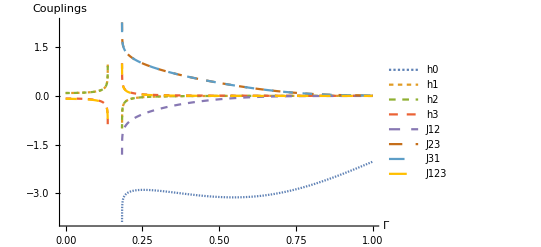

```mathematica
dash=Table[AbsoluteDashing[i],{i,1,8}];
Plot[Evaluate @ Table[Indexed[v[q,p,Γ]/.{Γ->0.1,q->2},i],{i,8}],{p,0,1},PlotLegends->vLegend,AxesLabel->{"Γ","Couplings"},PlotStyle->dash, PlotRange->All]
```

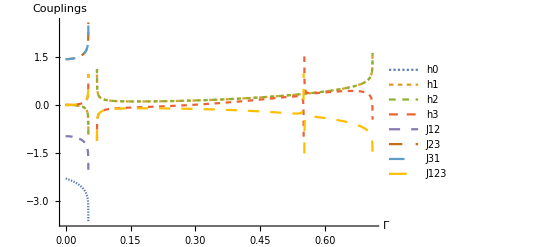

Google Drive/Random circuits/Pics/ru_p_0.1_q2.pdf

```mathematica
dash=Table[AbsoluteDashing[i],{i,1,8}];
Plot[Evaluate @ Table[Indexed[v[q,p,Γ]/.{p->0.1,q->2},i],{i,8}],{Γ,0,1},PlotLegends->vLegend,AxesLabel->{"Γ","Couplings"},LabelStyle->{FontSize->14},ImageSize->Scaled[.8],PlotStyle->dash, PlotRange->All]
Export["Google Drive/Random circuits/Pics/ru_p_0.1_q2.pdf",%]
```

```mathematica
v[q,p,Γ]/.{q->10000,Γ->0.2,p->0}
```

{-11.7399+0.785398 ⅈ,1.1703+0. ⅈ,1.1703+0. ⅈ,-1.12483+0. ⅈ,-1.66728+0.785398 ⅈ,6.28761-0.785398 ⅈ,6.28761-0.785398 ⅈ,-1.15514+0. ⅈ}

## Scraps:

```mathematica
w3[-1,-1,1,q,p,Γ]
w3[1,1,-1,q,p,Γ]
w3[-1,1,1,q,p,Γ]
w3[1,-1,-1,q,p,Γ]
```

((((1-p)^2 q+p^2 q) (1-Γ)^2-(((1-p)^2+p^2) q^2 Γ^2)/(-1+q^2))^2)/(-1+q^4)-(((p^2 q+(1-p)^2 q^2) (1-Γ)^2+(((1-p)^2+p^2) q^2 Γ^2)/(-1+q^2))^2)/(q^2 (-1+q^4))

((((1-p)^2 q+p^2 q) (1-Γ)^2-(q (p^2+(1-p)^2 q) Γ^2)/(-1+q^2))^2)/(-1+q^4)-(((p^2 q+(1-p)^2 q^2) (1-Γ)^2+(q^3 (p^2+(1-p)^2 q) Γ^2)/(-1+q^2))^2)/(q^2 (-1+q^4))

-(((p^2 q+(1-p)^2 q^2) (1-Γ)^2+(((1-p)^2+p^2) q^2 Γ^2)/(-1+q^2)) (((1-p)^2 q+p^2 q) (1-Γ)^2-(q (p^2+(1-p)^2 q) Γ^2)/(-1+q^2)))/(q^2 (-1+q^4))+((((1-p)^2 q+p^2 q) (1-Γ)^2-(((1-p)^2+p^2) q^2 Γ^2)/(-1+q^2)) ((p^2 q+(1-p)^2 q^2) (1-Γ)^2+(q^3 (p^2+(1-p)^2 q) Γ^2)/(-1+q^2)))/(-1+q^4)

(((p^2 q+(1-p)^2 q^2) (1-Γ)^2+(((1-p)^2+p^2) q^2 Γ^2)/(-1+q^2)) (((1-p)^2 q+p^2 q) (1-Γ)^2-(q (p^2+(1-p)^2 q) Γ^2)/(-1+q^2)))/(-1+q^4)-((((1-p)^2 q+p^2 q) (1-Γ)^2-(((1-p)^2+p^2) q^2 Γ^2)/(-1+q^2)) ((p^2 q+(1-p)^2 q^2) (1-Γ)^2+(q^3 (p^2+(1-p)^2 q) Γ^2)/(-1+q^2)))/(q^2 (-1+q^4))

```mathematica
Expand[(((1-p)^2 q+p^2 q) (1-Γ)^2-(((1-p)^2+p^2) q^2 Γ^2)/(-1+q^2))^2-((p^2 +(1-p)^2 q) (1-Γ)^2+(((1-p)^2+p^2) q Γ^2)/(-1+q^2))^2,q]
Expand[(((1-p)^2 q+p^2 q) (1-Γ)^2-(q (p^2+(1-p)^2 q) Γ^2)/(-1+q^2))^2-((p^2 +(1-p)^2 q) (1-Γ)^2+(q^2 (p^2+(1-p)^2 q) Γ^2)/(-1+q^2))^2,q]
Expand[-((p^2 +(1-p)^2 q) (1-Γ)^2+(((1-p)^2+p^2) q Γ^2)/(-1+q^2)) (((1-p)^2 +p^2 ) (1-Γ)^2-((p^2+(1-p)^2 q) Γ^2)/(-1+q^2))+(((1-p)^2 q+p^2 q) (1-Γ)^2-(((1-p)^2+p^2) q^2 Γ^2)/(-1+q^2)) ((p^2 q+(1-p)^2 q^2) (1-Γ)^2+(q^3 (p^2+(1-p)^2 q) Γ^2)/(-1+q^2)),q]
Expand[((p^2 q+(1-p)^2 q^2) (1-Γ)^2+(((1-p)^2+p^2) q^2 Γ^2)/(-1+q^2)) (((1-p)^2 q+p^2 q) (1-Γ)^2-(q (p^2+(1-p)^2 q) Γ^2)/(-1+q^2))-(((1-p)^2 +p^2 ) (1-Γ)^2-(((1-p)^2+p^2) q Γ^2)/(-1+q^2)) ((p^2 +(1-p)^2 q) (1-Γ)^2+(q^3 (p^2+(1-p)^2 ) Γ^2)/(-1+q^2)),q]
```

-p^4 (1-Γ)^4-2 (1-p)^2 p^2 q (1-Γ)^4+2 (1-p)^2 p^2 q^2 (1-Γ)^4+p^4 q^2 (1-Γ)^4-(2 p^2 ((1-p)^2+p^2) q (1-Γ)^2 Γ^2)/(-1+q^2)-(2 (1-p)^2 ((1-p)^2+p^2) q^2 (1-Γ)^2 Γ^2)/(-1+q^2)-(2 (1-p)^2 ((1-p)^2+p^2) q^3 (1-Γ)^2 Γ^2)/(-1+q^2)-(2 p^2 ((1-p)^2+p^2) q^3 (1-Γ)^2 Γ^2)/(-1+q^2)-(((1-p)^2+p^2)^2 q^2 Γ^4)/((-1+q^2)^2)+(((1-p)^2+p^2)^2 q^4 Γ^4)/((-1+q^2)^2)

-p^4 (1-Γ)^4-2 (1-p)^2 p^2 q (1-Γ)^4+2 (1-p)^2 p^2 q^2 (1-Γ)^4+p^4 q^2 (1-Γ)^4-(2 (1-p)^2 p^2 q^2 (1-Γ)^2 Γ^2)/(-1+q^2)-(4 p^4 q^2 (1-Γ)^2 Γ^2)/(-1+q^2)-(2 (1-p)^4 q^3 (1-Γ)^2 Γ^2)/(-1+q^2)-(6 (1-p)^2 p^2 q^3 (1-Γ)^2 Γ^2)/(-1+q^2)-(2 (1-p)^4 q^4 (1-Γ)^2 Γ^2)/(-1+q^2)+(p^4 q^2 Γ^4)/((-1+q^2)^2)+(2 (1-p)^2 p^2 q^3 Γ^4)/((-1+q^2)^2)+((1-p)^4 q^4 Γ^4)/((-1+q^2)^2)-(p^4 q^4 Γ^4)/((-1+q^2)^2)-(2 (1-p)^2 p^2 q^5 Γ^4)/((-1+q^2)^2)-((1-p)^4 q^6 Γ^4)/((-1+q^2)^2)

-p^2 ((1-p)^2+p^2) (1-Γ)^4-(1-p)^2 ((1-p)^2+p^2) q (1-Γ)^4+(1-p)^2 p^2 q^2 (1-Γ)^4+p^4 q^2 (1-Γ)^4+(1-p)^4 q^3 (1-Γ)^4+(1-p)^2 p^2 q^3 (1-Γ)^4+(p^4 (1-Γ)^2 Γ^2)/(-1+q^2)+(2 (1-p)^2 p^2 q (1-Γ)^2 Γ^2)/(-1+q^2)-(((1-p)^2+p^2)^2 q (1-Γ)^2 Γ^2)/(-1+q^2)+((1-p)^4 q^2 (1-Γ)^2 Γ^2)/(-1+q^2)-(p^2 ((1-p)^2+p^2) q^3 (1-Γ)^2 Γ^2)/(-1+q^2)+((1-p)^2 p^2 q^4 (1-Γ)^2 Γ^2)/(-1+q^2)+(p^4 q^4 (1-Γ)^2 Γ^2)/(-1+q^2)-((1-p)^2 ((1-p)^2+p^2) q^4 (1-Γ)^2 Γ^2)/(-1+q^2)+((1-p)^4 q^5 (1-Γ)^2 Γ^2)/(-1+q^2)+((1-p)^2 p^2 q^5 (1-Γ)^2 Γ^2)/(-1+q^2)+(p^2 ((1-p)^2+p^2) q Γ^4)/((-1+q^2)^2)+((1-p)^2 ((1-p)^2+p^2) q^2 Γ^4)/((-1+q^2)^2)-(p^2 ((1-p)^2+p^2) q^5 Γ^4)/((-1+q^2)^2)-((1-p)^2 ((1-p)^2+p^2) q^6 Γ^4)/((-1+q^2)^2)

-p^2 ((1-p)^2+p^2) (1-Γ)^4-(1-p)^2 ((1-p)^2+p^2) q (1-Γ)^4+(1-p)^2 p^2 q^2 (1-Γ)^4+p^4 q^2 (1-Γ)^4+(1-p)^4 q^3 (1-Γ)^4+(1-p)^2 p^2 q^3 (1-Γ)^4+(p^2 ((1-p)^2+p^2) q (1-Γ)^2 Γ^2)/(-1+q^2)-(p^4 q^2 (1-Γ)^2 Γ^2)/(-1+q^2)+((1-p)^2 ((1-p)^2+p^2) q^2 (1-Γ)^2 Γ^2)/(-1+q^2)-(2 (1-p)^2 p^2 q^3 (1-Γ)^2 Γ^2)/(-1+q^2)+((1-p)^2 ((1-p)^2+p^2) q^3 (1-Γ)^2 Γ^2)/(-1+q^2)+(p^2 ((1-p)^2+p^2) q^3 (1-Γ)^2 Γ^2)/(-1+q^2)-(((1-p)^2+p^2)^2 q^3 (1-Γ)^2 Γ^2)/(-1+q^2)-((1-p)^4 q^4 (1-Γ)^2 Γ^2)/(-1+q^2)-(p^2 ((1-p)^2+p^2) q^3 Γ^4)/((-1+q^2)^2)-((1-p)^2 ((1-p)^2+p^2) q^4 Γ^4)/((-1+q^2)^2)+(((1-p)^2+p^2)^2 q^4 Γ^4)/((-1+q^2)^2)